1

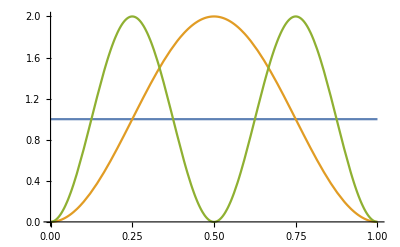

-Graphics3D-

1

```mathematica
ClearAll["Global`*"]
$Assumptions={n∈Integers,n≥0};
X[n_]:=Piecewise[{{1, n==0}, {1/2, True}}]

ϕ[n_][x_]:=Piecewise[{{Sin[n π x],n≠0},{1,n==0}}]/Sqrt[X[n]]
ψ[n_][x_,v_]:=ϕ[n][x]
Integrate[ϕ[n][x]^2,{x,0,1}]

Plot[Table[ϕ[n][x]^2,{n,0,2}]//Evaluate,{x,0,1}]



x0[v0_,x0_][t_]:=x0+v0 t
x0[v_,x_,t_]:=x0[v,x][-t]

Like[n_][x_,v_,t_]:=ϕ[n][x0[v,x,t]]^2
Plot3D[Like[3][x,v,0],{x,0,1},{v,-2,2}]

A[n_][x_,t_]:=(Like[n][x,-1,t]+Like[n][x,1,t])/Piecewise[{{2, n==0}, {(4 n π+Sin[2 n π t]-Sin[2 n π (1+t)])/(2 n π), True}}]
Integrate[A[n][x,t],{x,0,1}]

Manipulate[Plot[A[4][x,t],{x,0,1},PlotRange->{0,2}],{t,0,1}]
```

```mathematica
xDist=ProbabilityDistribution[ϕ[1][x],{x,0,1}]
ensemble=Array[x0[RandomChoice[{-3,3}],RandomVariate[xDist]]&,10]
```

ProbabilityDistribution[√2 Sin[x π],{x,0,1}]

{x0[3,0.481893],x0[-3,0.579412],x0[3,0.581032],x0[-3,0.874514],x0[3,0.0912497],x0[-3,0.74901],x0[-3,0.665168],x0[-3,0.535722],x0[3,0.606254],x0[-3,0.143637]}

```mathematica
RandomVariate[xDist]
```

0.612701